# Motorbike net2 & net3

## Set Environment

```mathematica
home = "/home/lichao/scratch/pami/";workdir = "/home/lichao/git/geonb/";SetDirectory[workdir];
```

```mathematica
prefix = "motor_train_";suffix="_64";
```

```mathematica
Needs["Posecpp`","posecpp_network.wl"];
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{308209,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

297

1311

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{346,378,356,220,251,379,72,250,168,162,14,148,56,268,111,135,288,312,344,241,260,54,40,156,169,271,21,144,66,130,46,256,36,15,296,84,26,380,328,133,105,45,33,210,150,191,174,119,69,231,198,93,47,29,176,51,206,149,64,41,16,3,316,345,301,209,182,177,163,147,129,370,83,61,30,22,5,0,299,286,278,365,240,238,236,320,315,211,203,195,180,155,153,273,146,109,82,63,62,55,38,31,368,137,73,6,4,2,342,335,327,302,267,258,237,235,230,222,364,215,214,205,161,157,145,142,126,124,118,117,376,100,97,80,67,57,343,332,323,322,319,300,297,294,291,285,284,257,242,228,224,193,186,173,166,262,204,187,385,140,136,122,106,85,75,68,53,35,34,32,12,10,7,369,352,349,347,334,325,309,305,304,292,287,283,281,249,247,246,234,208,207,199,197,196,188,184,179,178,175,165,225,160,139,112,110,103,102,99,96,90,79,77,74,60,59,128,52,43,24,23,361,359,354,338,336,333,330,318,314,313,307,306,298,295,293,289,275,274,270,269,263,261,255,254,252,243,233,227,389,218,217,216,213,202,201,171,167,351,340,158,154,141,138,132,121,116,115,107,98,94,92,89,88,86,78,76,71,65,49,48,42,37,28,20,19,18,9}

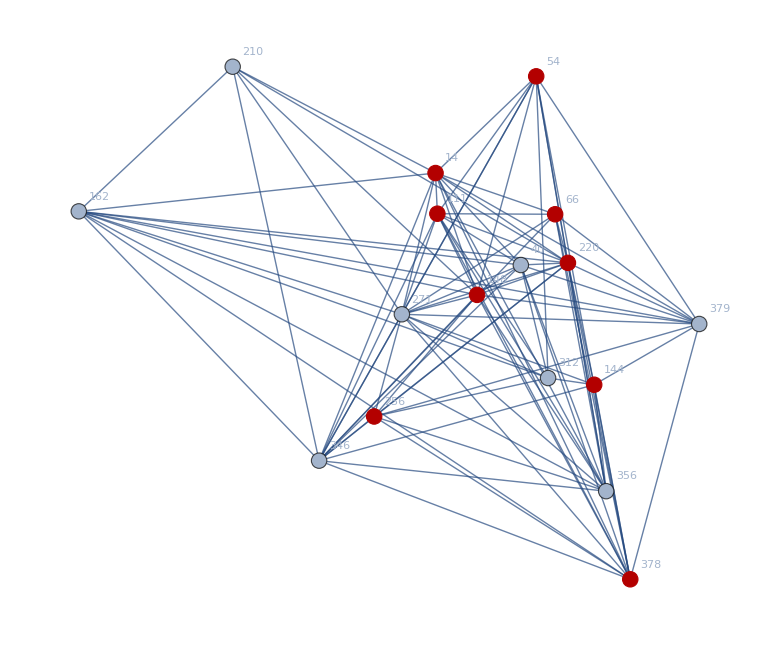

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

/home/lichao/scratch/pami/motor_train_net2_el_64.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_03_02"<>suffix<>".txt"]
```

{8<->695,17<->274,17<->352,17<->780,26<->308,26<->587,48<->705,53<->134,68<->100,68<->677,68<->785,75<->456,75<->720,79<->673,80<->371,100<->257,100<->453,100<->785,106<->189,106<->253,106<->567,107<->306,107<->794,125<->271,137<->304,141<->480,154<->284,156<->507,156<->580,189<->210,189<->253,189<->567,190<->310,212<->757,223<->748,228<->357,228<->677,228<->705,228<->785,230<->757,236<->266,239<->363,241<->342,241<->583,253<->567,257<->453,261<->637,266<->668,267<->757,276<->298,304<->349,304<->587,323<->787,342<->583,371<->689,433<->791,452<->583,453<->566,453<->785,469<->600,471<->787,497<->595,518<->689,537<->552,567<->668,593<->640,617<->791,677<->785,748<->791,780<->786}

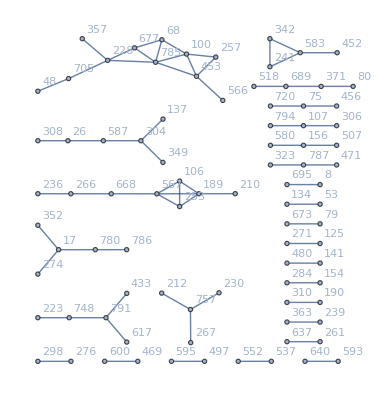

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
```

87

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{566,453,100,257,785,68,228,677,357,705,48},{266,236,668,567,106,189,253,210},{349,304,137,587,26,308},{617,791,433,748,223},{352,17,274,780,786},{212,757,230,267},{342,241,583,452},{80,371,689,518},{156,507,580},{794,107,306},{456,75,720},{323,787,471},{595,497},{261,637},{190,310},{8,695},{134,53},{125,271},{154,284},{593,640},{673,79},{480,141},{363,239},{537,552},{469,600},{276,298}}

```mathematica
comp3//Length
```

22

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
```

```mathematica
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

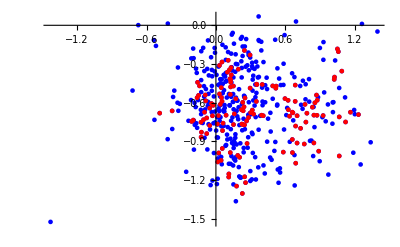

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,{Keys[gx],VertexList[g3]},{2}],PlotStyle->{Blue,Red}]
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

/home/lichao/scratch/pami/motor_train_global_summary_64.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{2,69,98,107,126,144,153,154,231,249,298,315,468,554},{1,32,109,118,212,225,311,347,364,365,370,485,538,597},{19,26,128,203,218,280,306,383,387,434,464,483,632},{51,81,239,267,290,327,406,508,636},{0,222,250,273,326,424,555},{155,209,300,312,534},{328,338,397,399,451},{410,446,593,642},{178,431,452},{93,214,512},{85,156,268},{137,200,232},{38,278,491},{174,179,474},{114,145,333},{258,292},{163,252},{65,284},{725,793},{24,83},{486,634},{111,167},{308,661},{566,635},{166,613},{321,360},{70,230},{402,498},{61,395},{62,187},{471,643},{14,349},{416,419}}

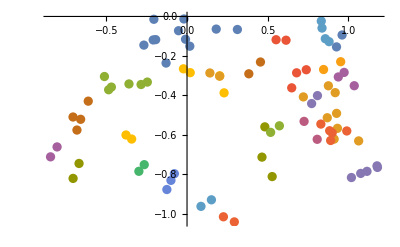

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}]]
```

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Mean[gs]
```

0.417891

```mathematica
StandardDeviation[gs]
```

0.130251

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

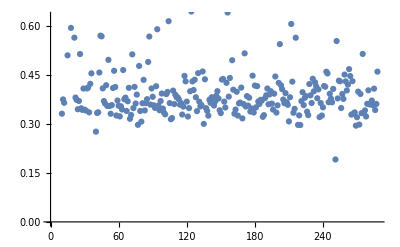

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

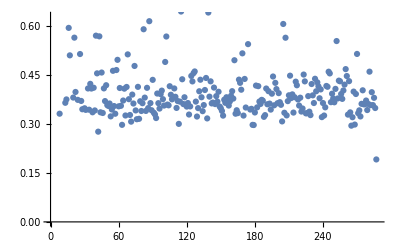

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

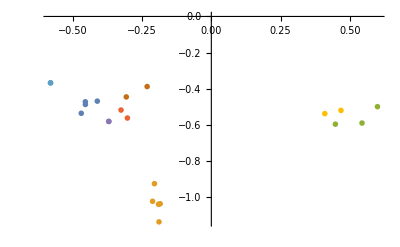

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{48,68,100,228,257,357,453,566,677,705,785},{106,189,210,236,253,266,567,668},{26,137,304,308,349,587},{223,433,617,748,791},{17,274,352,780,786},{212,230,267,757},{241,342,452,583},{80,371,518,689},{156,507,580},{107,306,794},{75,456,720},{323,471,787},{497,595},{261,637},{190,310},{8,695},{53,134},{125,271},{154,284},{593,640},{79,673},{141,480},{239,363},{537,552},{469,600},{276,298}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],gs[#]}&,voroComms,{2}]
```

{{-0.276837,-0.122914,0.448518},{0.692641,0.286039,0.421145},{-0.581895,0.153888,0.377355},{0.652488,0.338312,0.493972},{0.885379,0.555317,0.458643},{-0.87881,0.296319,0.426273},{0.608688,-0.162887,0.487311},{-0.148456,0.0538548,0.511929},{0.621268,-0.0481003,0.724317},{0.156635,0.360057,0.670611},{0.255947,-0.127591,0.867448},{-0.451054,0.485822,0.699878},{0.653053,0.0023465,0.494105},{0.189614,0.0005485,1.15444},{-0.487043,0.563733,0.410021},{0.744673,-0.0757105,0.399864},{0.003058,0.125756,0.338246},{0.332525,0.35819,0.426416},{0.080002,0.849727,0.359154},{0.373085,0.0037455,0.835914},{0.147782,-0.0107095,0.543412},{-0.074516,0.753446,0.386824},{-0.577493,0.395159,0.43293},{-1.0342,0.479229,0.415645},{-0.965389,0.506677,0.554067},{0.327508,-0.136541,0.511569}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

26

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

/home/lichao/scratch/pami/motor_train_voro_centers_64.txt